# Boundary Lines and Centroids

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\nathanm\OneDrive\dinosaur research\fabbri et al rebuttal\mathematica for github

```mathematica
CloseKernels[];
LaunchKernels[]
```

{Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local,Local}

```mathematica
<<"phylo for mathematica\\PollyPhylogenetics6.6.m"
```

Phylogenetics for Mathematica 6.6
(c) P. David Polly, 26 November 2022

## Data Files

### Files with data

```mathematica
allcsvfiles = FileNames["*.csv",{"ds1 full"},4];
```

```mathematica
boundarypos = Flatten[Table[Position[Map[FileNameSplit,allcsvfiles],{_,_,"bs",StringJoin["set_",ToString[i]],"BOUNDARY_LINE_COEFFS.csv"}],{i,1,100}],1];
```

```mathematica
datasetpos = Flatten[Table[Position[Map[FileNameSplit,allcsvfiles],{_,_,"bs",StringJoin["set_",ToString[i]],StringJoin["femur_set_",ToString[i],".csv"]}],{i,1,100}],1];
```

```mathematica
boundarylinefiles = Extract[allcsvfiles,boundarypos];
```

```mathematica
datasetfiles = Extract[allcsvfiles,datasetpos];
```

### Decision boundaries

```mathematica
boundraw = Map[Drop[#,1]&,Map[Drop[Import[#],1]&,boundarylinefiles],{2}];
```

### Datasets

```mathematica
datasetsraw = Map[Drop[Import[#],1]&,datasetfiles];
```

```mathematica
datasetsraw[[1,-1]]
```

{Baryonyx.3,Nathan et al,NA,D same as Fabbri Cg scanned Cg low,17,17,129.4,127,0.767,154,2.18752,0,UNKNOWN,UNKNOWN,UNKNOWN}

```mathematica
datasettaxa = Map[First,datasetsraw,{2}];
```

```mathematica
datasettaxa[[1]]
```

{Monodelphis_domestica,Felis_felis,Rangifer_tarandus,Elephas_maximus,Rangifer_tarandus.1,Lacerta_viridis,Euroscaptor_micrura,Okapia_johnstoni,Rangifer_tarandus.2,Uncia_uncia,Elomeryx_borbonicus_,Procavia_capensis,Atlantisia_rogersi,Atlantisia_rogersi.1,Dromaius_,Meles_meles,Lacerta_viridis.1,Lacerta_viridis.2,Tenrec_ecaudatus,Hemiechinus_azurites,Rhinoceros_sondaicus,Lacerta_viridis.3,Monodelphis_domestica.1,Loxodonta_africana,Taxidea_taxus,Nyctereutes_procyonoides,Rupicapra_rupicapra,Syncerus_caffer,Cephalophus_silvicultor,Felis_felis.1,Okapia_johnstoni.1,Alces_americanus,Rattus_rattus,Lama_guanicoe,Euroscaptor_micrura.1,Giraffa_camelopardalis,Monodelphis_domestica.2,Tenrec_ecaudatus.1,Tamandua_tetradactyla,Giraffa_camelopardalis.1,Sphenodon_punctatus,Rynochetus_jubatus,Mus_musculus,Rhynchocyon_petersi,Bison_bonasus,Apteryx_owenii_,Rangifer_tarandus.3,Brachyodus_onoideum,Capreolus_capreolus,Megaloceros_sp,Hemiechinus_azurites.1,Strigiops_habroptilus,Raphus,Lacerta_viridis.4,Rattus_rattus.1,Rattus_rattus.2,Cephalophus_silvicultor.1,Cephalophus_silvicultor.2,Placondontia_indet,Rodhocetus,Palaeospheniscus,Anarosaurus,Protochampsidae,Desmostylus_hesperus,Serpianosaurus,Placondontia_indet.1,Palaeospheniscus.1,Nanophoca_vitulinoides,Hexaprotodon_garyam,Nothosaurus_mirabilis_1,Remingtonocetus,Chironectes_minimus,Metryorhynchus,Plesiosaurus,Desmana_moschata,Alligator,Hydromys_chrysogaster,Dyrosaurid,Maiacetus,Anarosaurus.1,Micropotamogale_euwenzorii,Serpianosaurus.1,Nothosaurus_568,Basilosaurus,Nothosaurus_giganteus,large_eocene_stem_penguin,Ornithorhynchus_anatinus,Caiman_yacare,Nothosaurus_102,Rhaeticosaurus,Micropotamogale_euwenzorii.1,Ichtyosaurus_,Remingtonocetus.1,Chapsosaurus_,Callophoca_obscura,Rhaeticosaurus.1,Palaeospheniscus.2,Spheniscus,Castor_fiber,Palaeospheniscus.3,Caiman_yacare.1,Desmana_moschata.1,Nothosaurus_568.1,Ichtyosaurus_.1,Palaeospheniscus.4,Rhaeticosaurus.2,Maiacetus.1,Ichtyosaur_sp,Hexaprotodon_garyam.1,Small_Eocene_penguin,Basilosaurus.1,Neusticosaurus,Small_Eocene_penguin.1,Plesiosaurus.1,Small_Eocene_penguin.2,Anarosaurus.2,Nothosaurus_568.2,Baryonyx,Spinosaurus_,Suchomimus,Spinosaurus_.1,Spinosaurus_.2,Spinosaurus_.3,Spinosaurus_.4,Spinosaurus_.5,Spinosaurus_.6,Spinosaurus_.7,Spinosaurus_.8,Spinosaurus_.9,Spinosaurus_.10,Spinosaurus_.11,Suchomimus.1,Suchomimus.2,Suchomimus.3,Baryonyx.1,Baryonyx.2,Baryonyx.3}

## General Functions

```mathematica
cleanmatrix[wraw_]:= Map[Drop[#,1]&,Drop[wraw,1]];
```

```mathematica
makenmatrix[w_]:=
Module[{invw,eval,evec,tevec,invtevec,dig,n1,dexp,divnum},
invw = Inverse[w];
{eval,evec} = Eigensystem[invw];
tevec = Transpose[evec];
invtevec = Inverse[tevec];
dig = DiagonalMatrix[Sqrt[eval]];
n1 = tevec.dig.invtevec;
dexp = 1/Length[w];
divnum = Det[n1]^dexp;
n1/divnum
];
```

```mathematica
matrix4lambda[mat_,lamobs_]:=
Module[{dm,nd},
dm = DiagonalMatrix[Diagonal[mat]];
nd = (mat - dm)/lamobs;
{dm,nd}
]
```

```mathematica
matrixsquareroot[mat_]:=
Module[{invw,eval,evec,tevec,invtevec,dig},
{eval,evec} = Eigensystem[mat];
tevec = Transpose[evec];
invtevec = Inverse[tevec];
dig = DiagonalMatrix[Sqrt[eval]];
tevec.dig.invtevec
];
```

## Plot Functions

```mathematica
logticks =  Join[Table[{Log[10^k],10^k},{k,0,3}],Flatten[Table[{Log[j*10^k],""},{k,0,3},{j,2,9,1}],1]];
```

```mathematica
log10ticks = Join[Table[{k,10^k},{k,0,3}],Flatten[Table[{Log[10,j*10^k],""},{k,0,3},{j,2,9,1}],1]];
```

```mathematica
xlines[pt_,armlen_]:= {Line[{pt-{armlen,0},pt+{armlen,0}}],Line[{pt-{0,armlen},pt+{0,armlen}}]};
```

```mathematica
xlines2[pt_,{armlen1_,armlen2_}]:= {Line[{pt-{armlen1,0},pt+{armlen1,0}}],Line[{pt-{0,armlen2},pt+{0,armlen2}}]};
```

```mathematica
topticklabel[min_,max_,lab_]:= {{min,Style[lab,"Arial",12,Bold],0}};
```

```mathematica
mswordsize = 6.5*72;
```

```mathematica
shadeopacity = 0.3;
pointopacity = 0.6;
```

## Phylogenetic tree

### Rib

```mathematica
ribtreeraw = Import["tree_ribs_final.nex","Lines"];
```

```mathematica
ribtreeindex = Map[DeleteCases[#,""]&,StringSplit[ribtreeraw[[5;;179]],Whitespace..|"'"|","]];
```

```mathematica
ribtreenamerules = Map[StringJoin[#[[1]],":"]-> StringJoin[#[[2]],":"]&,ribtreeindex];
```

```mathematica
ribtreess = StringSplit[ribtreeraw[[3]],"tree:"|"[%"];
```

```mathematica
rtt =StringJoin[ ribtreess[[2]],";"];
```

```mathematica
ribtree = StringReplace[ StringDelete[rtt," "],ribtreenamerules];
```

```mathematica
(*DrawNewickTree[ribtree]*)
```

```mathematica
wribraw=PhylogeneticMatrices[ribtree][[1]];
```

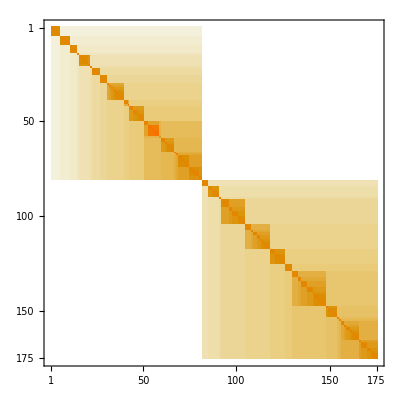

```mathematica
MatrixPlot[cleanmatrix[wribraw]]
```

```mathematica
allnamesinribtree = Drop[wribraw[[1]],1];
```

### Femur

```mathematica
femurtreeraw = Import["tree_femur_final.nex","Lines"];
```

```mathematica
femurtreess =StringSplit[femurtreeraw[[3]],"R]"|";"];
```

```mathematica
femurtree =StringJoin[StringDelete[femurtreess[[2]]," "],";"];
```

```mathematica
wfemurraw=PhylogeneticMatrices[femurtree][[1]];
```

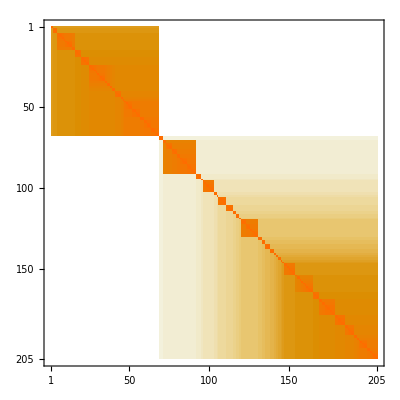

```mathematica
MatrixPlot[cleanmatrix[wfemurraw]]
```

```mathematica
allnamesinfemurtree = Drop[wfemurraw[[1]],1];
```

## Data with phylogeny

```mathematica
phyloadjustpts[{class1_,class2_,class3_}, tree_,plam_]:=
Module[{rawd,alldata,lens,indicator,names,namebyclass,datapts,databyclass,dtree,wmatraw,namesfromtree,wmat,
wmatdia,wmatoffdia,wwl,nwl,datpts,datanames,nameorder,indicatoradj,datptsinorder,datadj,datadjbyclass,namesinorderclass},
rawd = {class1,class2,class3};
alldata = Flatten[rawd,1];
lens = Map[Length,rawd];
indicator ={Join[Table[1,{lens[[1]]}],Table[0,{lens[[2]]}],Table[0,{lens[[3]]}]],Join[Table[0,{lens[[1]]}],Table[1,{lens[[2]]}],Table[0,{lens[[3]]}]],Join[Table[0,{lens[[1]]}],Table[0,{lens[[2]]}],Table[1,{lens[[3]]}]]};
names = alldata[[All,1]];
namebyclass = Table[Pick[names,indicator[[i]],1],{i,1,3}];
datapts = alldata[[All,{1,11,9}]];
databyclass = Table[Pick[datapts,indicator[[i]],1],{i,1,3}];
dtree = PruneTree[Flatten[databyclass[[All,All,1]]],tree];
wmatraw = PhylogeneticMatrices[dtree][[1]];
namesfromtree = Drop[wmatraw[[1]],1];
wmat = cleanmatrix[wmatraw];
{wmatdia, wmatoffdia}= matrix4lambda[wmat,1];
wwl = wmatdia + plam*wmatoffdia;
nwl = makenmatrix[wwl];
datpts= Flatten[databyclass[[All, All,{2,3}]],1];
datanames =  Flatten[databyclass[[All,All,1]],1];
nameorder = FindPermutation[datanames,namesfromtree];
indicatoradj = Map[Permute[#,nameorder]&,indicator];
datptsinorder = Permute[datpts,nameorder];
datadj = nwl.datptsinorder;
datadjbyclass = Table[Pick[datadj,indicatoradj[[i]],1],{i,1,3}];
namesinorderclass =  Table[Pick[namesfromtree,indicatoradj[[i]],1],{i,1,3}];
{datadjbyclass,namesinorderclass}
];
```

### Femur (new)

```mathematica
spinonames2 = {"Su","Ba","Sp"};
```

```mathematica
femurallraw  = Import["femur compactness all.csv"];
```

```mathematica
{Range[Length[femurallraw[[1]]]],femurallraw[[1]]}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
taxa | Reference | Specimen | Type of data | AFA | ALA | FAD | LAD | Global compactness | MD (mm) | MD log | Flying | Diving | finest.category | diving.or.not

```mathematica
femurallraw1 = Drop[femurallraw,1];
```

```mathematica
femurf0raw = Pick[femurallraw1,femurallraw1[[All,12]],0];
```

```mathematica
namesnotintree = Complement[femurf0raw[[All,1]],allnamesinfemurtree]
```

{Rhinoceros_unicornis}

```mathematica
badpos = Flatten[Map[Position[femurf0raw[[All,1]],#]&,namesnotintree],1]
```

{{112}}

```mathematica
femurf0raw1 = Delete[femurf0raw,badpos];
```

```mathematica
femurf0d0raw =  Pick[femurf0raw1,femurf0raw1[[All,13]],0];
```

```mathematica
femurf0d2raw =  Pick[femurf0raw1,femurf0raw1[[All,13]],2];
```

```mathematica
femurdinos = Pick[femurf0raw1,femurf0raw1[[All,13]],"UNKNOWN"];
```

```mathematica
fwdinosadj = phyloadjustpts[{femurf0d0raw,femurf0d2raw,femurdinos}, femurtree,0.06];
```

```mathematica
Position[fwdinosadj[[2,3]],"Spinosaurus_"]
```

{{17}}

```mathematica
Position[fwdinosadj[[2,3]],"Baryonyx"]
```

{{15}}

```mathematica
Position[fwdinosadj[[2,3]],"Suchomimus"]
```

{{16}}

```mathematica
femurspinoadjpts = fwdinosadj[[1,3,{16,15,17}]]
```

{{1.47478,0.433565},{1.58328,0.631825},{1.30225,0.72605}}

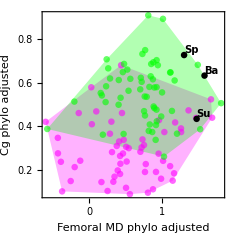

```mathematica
femuradjplot = Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,2]]]}},
Table[{Black,PointSize[.02],Point[femurspinoadjpts[[k]]]},{k,1,Length[spinonames2]}],
Table[Text[Style[spinonames2[[k]],Black,10,Italic,Bold],femurspinoadjpts[[k]],{-1,-1}],{k,1,Length[spinonames2]}]
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},FrameLabel-> {"Femoral MD phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

```mathematica
fm1 = Mean[fwdinosadj[[1,1]]]
```

{0.539852,0.29243}

```mathematica
fm2=Mean[fwdinosadj[[1,2]]]
```

{0.732264,0.555206}

```mathematica
femurrange =Map[MinMax,Transpose[Join[fwdinosadj[[1,1]],fwdinosadj[[1,2]]]]]
```

{{-0.602994,1.81182},{0.0883727,0.908312}}

```mathematica
frrat =(femurrange[[2,2]]-femurrange[[2,1]])/(femurrange[[1,2]]-femurrange[[1,1]])
```

0.339545

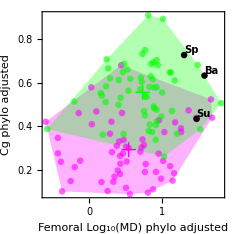

```mathematica
femuradjplot2 = Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[fwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,fwdinosadj[[1,2]]]}},
{Magenta,Thick, xlines2[fm1,0.1*{1,frrat}]},
{Green,Thick, xlines2[fm2,0.1*{1,frrat}]},
Table[{Black,PointSize[.02],Point[femurspinoadjpts[[k]]]},{k,1,Length[spinonames2]}],
Table[Text[Style[spinonames2[[k]],Black,10,Italic,Bold],femurspinoadjpts[[k]],{-1,-1}],{k,1,Length[spinonames2]}]
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"A"]&}},FrameLabel-> {"Femoral Log_10(MD) phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

### Rib (new)

```mathematica
ribspinonames2 = {"Ba","Sp"};
```

```mathematica
riballraw  = Import["ribs compactness all.csv"];
```

```mathematica
riballraw1 = Drop[riballraw,1];
```

```mathematica
ribf0raw = Pick[riballraw1,riballraw1[[All,12]],0];
```

```mathematica
namesnotinribtree = Complement[ribf0raw[[All,1]],allnamesinribtree]
```

{Capra_aegagrus}

```mathematica
ribbadpos = Flatten[Map[Position[ribf0raw[[All,1]],#]&,namesnotinribtree],1]
```

{{76}}

```mathematica
ribf0raw1 = Delete[ribf0raw,ribbadpos];
```

```mathematica
ribf0d0raw =  Pick[ribf0raw1,ribf0raw1[[All,13]],0];
```

```mathematica
ribf0d2raw =  Pick[ribf0raw1,ribf0raw1[[All,13]],2];
```

```mathematica
ribdinos = Pick[ribf0raw1,ribf0raw1[[All,13]],"UNKNOWN"];
```

```mathematica
ribdinos
```

{{Lourinhanosaurus,Waskow & Mateus (2017),ML 370,,11,12,155.7,145,0.631,11.3,1.05308,0,UNKNOWN,none,0},{Saltriovenator,Dal Sasso et al. (2018),MSNM V3664,,4,5,196.5,189.6,0.704,21.3,1.32838,0,UNKNOWN,none,0},{Baryonyx,This study,BMNH 9951,Thin section,13,13,129.4,127,0.921,42.2,1.62531,0,UNKNOWN,UNKNOWN,UNKNOWN},{Spinosaurus,This study,FSAC-KK 11888,Thin section,14,14,100.5,93.9,0.931,35.1,1.54531,0,UNKNOWN,UNKNOWN,UNKNOWN},{Charcarodontosaurid,Cullen et al. (2020),MMCh PV 65,,14,15,100.5,89.8,0.805,25.5,1.40654,0,UNKNOWN,none,0},{Alamosaurus,Woodward (2005),HW-R2,,18,18,72.1,66,0.523,82.6,1.91698,0,UNKNOWN,none,0},{Plateosaurus,Klein & Sander (),SMNS F 29,Thin section,3,3,227,208.5,0.513,17.1,1.233,0,UNKNOWN,none,0},{Spinophorosaurus_nigerensis,Houssaye et al. (2016),Ni 5.40-7ax,,7,8,170.3,166.1,0.68,64.3,1.80821,0,UNKNOWN,none,0},{Apatosaurus_sp,Houssaye et al. (2016),BYU 145,,11,12,155.7,145,0.8,52.3,1.7185,0,UNKNOWN,none,0},{Diplodocus_sp,Houssaye et al. (2016),CMC 9932 ,,11,12,155.7,145,0.85,35,1.54407,0,UNKNOWN,none,0},{Brachiosaurus_sp,Houssaye et al. (2016),FMNH 25107,,11,12,155.7,145,0.84,95,1.97772,0,UNKNOWN,none,0},{Miragaia_longicollum,Houssaye et al. (2016),ML 433A ,,12,12,152.1,145,0.79,35,1.54407,0,UNKNOWN,none,0}}

```mathematica
rwdinosadj = phyloadjustpts[{ribf0d0raw,ribf0d2raw,ribdinos}, ribtree,0.07];
```

```mathematica
Position[rwdinosadj[[2,3]],"Spinosaurus"]
```

{{9}}

```mathematica
Position[rwdinosadj[[2,3]],"Baryonyx"]
```

{{8}}

```mathematica
Position[rwdinosadj[[2,3]],"Suchomimus"]
```

{}

```mathematica
ribspinonames2
```

{Ba,Sp}

```mathematica
ribspinoadjpts = rwdinosadj[[1,3,{8,9}]]
```

{{1.38577,0.754878},{1.30351,0.76516}}

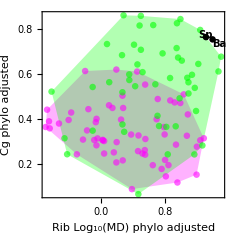

```mathematica
ribadjplot =Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,2]]]}},
Table[{Black,PointSize[.02],Point[ribspinoadjpts[[k]]]},{k,1,Length[ribspinonames2]}],
Table[Text[Style[ribspinonames2[[k]],Black,10,Italic,Bold],ribspinoadjpts[[k]]+{{0,0},{0,.01}}[[k]],{{-1,1},{0,-1}}[[k]]],{k,1,Length[ribspinonames2]}]
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},FrameLabel-> {"Rib Log_10(MD) phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

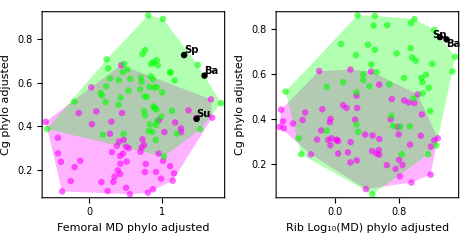

```mathematica
fig1xxplot = GraphicsGrid[{{femuradjplot,ribadjplot}},Spacings->0,ImageSize->mswordsize]
```

```mathematica
rm1 = Mean[rwdinosadj[[1,1]]]
```

{0.341513,0.343684}

```mathematica
rm2=Mean[rwdinosadj[[1,2]]]
```

{0.643651,0.557606}

```mathematica
ribrange =Map[MinMax,Transpose[Join[rwdinosadj[[1,1]],rwdinosadj[[1,2]]]]]
```

{{-0.6892,1.49241},{0.0655582,0.862263}}

```mathematica
rrrat =(ribrange[[2,2]]-ribrange[[2,1]])/(ribrange[[1,2]]-ribrange[[1,1]])
```

0.365191

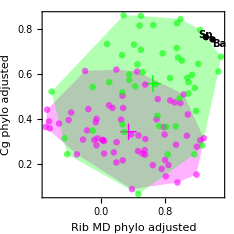

```mathematica
ribadjplot2 =Graphics[{
{Magenta,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,1]]]]]}},
{Green,{Opacity[shadeopacity],Polygon[MeshCoordinates[ConvexHullRegion[rwdinosadj[[1,2]]]]]}},
{Magenta,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,1]]]}},
{Green,{Opacity[pointopacity],PointSize[.02],Map[Point,rwdinosadj[[1,2]]]}},
{Magenta,Thick, xlines2[rm1,0.1*{1,rrrat}]},
{Green,Thick, xlines2[rm2,0.1*{1,rrrat}]},
Table[{Black,PointSize[.02],Point[ribspinoadjpts[[k]]]},{k,1,Length[ribspinonames2]}],
Table[Text[Style[ribspinonames2[[k]],Black,10,Italic,Bold],ribspinoadjpts[[k]]+{{0,0},{0,.01}}[[k]],{{-1,1},{0,-1}}[[k]]],{k,1,Length[ribspinonames2]}],
},AspectRatio->1,PlotRange-> All,PlotRangePadding-> Scaled[0.05],Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,topticklabel[#1,#2,"B"]&}},FrameLabel-> {"Rib MD phylo adjusted","Cg phylo adjusted"},FrameStyle-> Directive[Black,"Arial",10],ImageSize->mswordsize/2]
```

```mathematica
Sqrt[(rm1-rm2).(rm1-rm2)]
```

0.370203

```mathematica
StandardDeviation[Join[Map[# -rm1&,rwdinosadj[[1,1]]],Map[# -rm1&,rwdinosadj[[1,2]]]]]
```

{0.532597,0.186505}

```mathematica
femurf0d0andf0d2 = Join[femurf0d0raw,femurf0d2raw];
indicatorf0d0andf0d2 = {Join[Table[1,{Length[femurf0d0raw]}],Table[0,{Length[femurf0d2raw]}]],
Join[Table[0,{Length[femurf0d0raw]}],Table[1,{Length[femurf0d2raw]}]]};
femurf0d0andf0d2names =femurf0d0andf0d2[[All,1]];
femurnamesbyclass = Table[Pick[femurf0d0andf0d2names,indicatorf0d0andf0d2[[i]],1],{i,1,2}];
femurdata = femurf0d0andf0d2[[All,{1,11,9}]];
femurdatabyclass = Table[Pick[femurdata,indicatorf0d0andf0d2[[i]],1],{i,1,2}];
```

```mathematica
femursets2 = {femurdatabyclass[[1,All,{2,3}]],femurdatabyclass[[2,All,{2,3}]],fwdinosadj[[1,1]],fwdinosadj[[1,2]]};
```

```mathematica
DistributeDefinitions[femursets2,fwdinosadj]
```

{femursets2,fwdinosadj}

```mathematica
femursetnames2 = {"F0D0","F0D2","F0D0: lam = 0.06","F0D2, lam = 0.06"};
```

```mathematica
ribf0d0andf0d2 = Join[ribf0d0raw,ribf0d2raw];
indicatorf0d0andf0d2rib = {Join[Table[1,{Length[ribf0d0raw]}],Table[0,{Length[ribf0d2raw]}]],
Join[Table[0,{Length[ribf0d0raw]}],Table[1,{Length[ribf0d2raw]}]]};
ribf0d0andf0d2names =ribf0d0andf0d2[[All,1]];
ribdata = ribf0d0andf0d2[[All,{1,11,9}]];
ribnamesbyclass = Table[Pick[ribf0d0andf0d2names,indicatorf0d0andf0d2rib[[i]],1],{i,1,2}];
ribdatabyclass = Table[Pick[ribdata,indicatorf0d0andf0d2rib[[i]],1],{i,1,2}];
```

```mathematica
ribsets2 = {ribdatabyclass[[1,All,{2,3}]],ribdatabyclass[[2,All,{2,3}]],rwdinosadj[[1,1]],rwdinosadj[[1,2]]};
```

```mathematica
DistributeDefinitions[ribsets2]
```

{ribsets2}

```mathematica
ribsetnames2 = {"F0D0","F0D2","F0D0: lam = 0.07","F0D2, lam = 0.07"};
```

## Bootstrap set centroids

```mathematica
pointrules = Table[Map[#[[1]]->#[[2]]&,Transpose[{fwdinosadj[[2,i]],fwdinosadj[[1,i]]}]],{i,1,3}];
```

```mathematica
datasetnames = Table[Map[StringReplace[#,"."~~__->""]&,Drop[datasettaxa[[i]],-20]],{i,1,Length[datasettaxa]}];
```

```mathematica
cents = Table[{Mean[Cases[datasetnames[[i]]/.pointrules[[1]],{_?NumberQ,_?NumberQ}]],Mean[Cases[datasetnames[[i]]/.pointrules[[2]],{_?NumberQ,_?NumberQ}]]},{i,1,Length[datasettaxa]}];
```

```mathematica
centroids = Map[Union,Map[Round[#*1000.]/1000.&,Transpose[cents],{2}]];
```

```mathematica
markers = {Graphics[{Thick,Line[{{-0.5,0},{0.5,0}}]},ImageSize->100],Graphics[{Thick,xlines[{0,0},0.5]},ImageSize-> 100],Graphics[{PointSize[.33],Point[{0,0}]},ImageSize->100]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
lp1 = Table[Map[{-#[[1]]/#[[2]],Mean[cents[[i]]].{#[[1]]/#[[2]],1}}&,boundraw[[i]]],{i,1,100}];lineparams = Union[Map[Round[#*1000]/1000.&,Flatten[lp1,1],{2}]];
```

```mathematica
mcentroids = Map[Mean,fwdinosadj[[1,{1,2}]]]
```

{{0.539852,0.29243},{0.732264,0.555206}}

```mathematica
pointranges = Map[MinMax,Transpose[Flatten[fwdinosadj[[1]],1]]]
```

{{-0.602994,2.24931},{0.0883727,0.908312}}

```mathematica
swl1 = SwatchLegend[{Black,Red},{"Centroid","Decision boundary"},LegendMarkers->{"Bubble","Line"} ,LegendMarkerSize->{{5,5},{10,5}},LegendMargins->0,LabelStyle-> Directive[10,Black,"Arial"]]
```

```mathematica
plotranges ={pointranges[[1]],MinMax[ Flatten[{femurspinoadjpts[[All,2]], Table[{{lineparams[[i]].{pointranges[[1,1]],1},lineparams[[i]].{pointranges[[1,2]],1}}},{i,Length[lineparams]}]}]]}
```

{{-0.602994,2.24931},{0.172354,0.72605}}

```mathematica
scales =Map[#[[2]]-#[[1]]&,plotranges]
```

{2.8523,0.553696}

```mathematica
Put[{femurspinoadjpts,mcentroids, pointranges ,centroids, lineparams},"boundary and centroid data"]
```

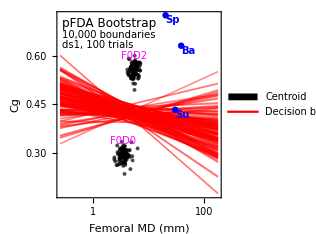

```mathematica
Graphics[{Table[{Red,Opacity[0.2],Thin,Line[{{pointranges[[1,1]],lineparams[[i]].{pointranges[[1,1]],1}},{pointranges[[1,2]],lineparams[[i]].{pointranges[[1,2]],1}}}]},{i,Length[lineparams]}],
{Black,Opacity[0.7],PointSize[.012],Map[Point,Flatten[centroids,1]]},
{Thick,Magenta,xlines2[mcentroids[[1]],0.02*scales],xlines2[mcentroids[[2]],0.02*scales]}},
FrameStyle-> Directive[10,Black,"Arial"],FrameLabel-> {"Femoral MD (mm)","Cg"},
PlotRange-> plotranges,PlotRangePadding->Scaled[0.03],PlotRangeClipping->True, AspectRatio-> 1,Frame-> True,FrameTicks-> {{Automatic,None},{log10ticks,topticklabel[#1,#2,"A"]&}},
Epilog->{Text[Style["pFDA Bootstrap",12,Black],Scaled[{0.03,0.97}],{-1,1}],
Text[Style["10,000 boundaries",10,Black],Scaled[{0.03,0.90}],{-1,1}],Text[Style["ds1, 100 trials",10,Black],Scaled[{0.03,0.85}],{-1,1}],
Text[Style["F0D2",10,Magenta,Italic,"Arial"],mcentroids[[2]]+{0,0.045},{0,-1}],
Text[Style["F0D0",10,Magenta,Italic,"Arial"],mcentroids[[1]]+{0,0.045},{0,-1}],
Inset[swl1,Scaled[{0.02,0.02}],{Left,Bottom}],
Table[{Blue,PointSize[.02],Point[femurspinoadjpts[[k]]]},{k,1,Length[spinonames2]}],
Table[Text[Style[spinonames2[[k]],Blue,10,Italic,Bold],femurspinoadjpts[[k]],{-1,1}],{k,1,Length[spinonames2]}]
}, ImageSize-> mswordsize/2]
```